1/2 (-c+d)

1/12 (c-d) L

1/2 (-c+d)

1/12 (-c+d) L

(c-d)/2

1/12 (c-d) L

(c-d)/2

1/12 (-c+d) L

((c+d)/2
1/12 (c-d) L
1/2 (-c-d)
1/12 (-c+d) L
-((c-d)^2 L^3)/(720 Iyy Ε))

(1/2 (-c-d)
1/12 (c-d) L
(c+d)/2
1/12 (-c+d) L
-((c-d)^2 L^3)/(720 Izz Ε))

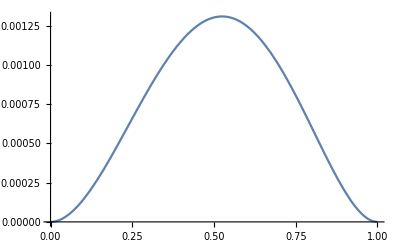

```mathematica
Clear[x,a,b,c,d]
u={u1,θ1,u2,θ2,1};
rep={u1->0,θ1->0,θ2->0,u2->0,a->0,b->0(*,c->0,d->0*)};
pn={1,x,x^2,x^3,x^4,x^5};
Muz=({{1, 0, 0, 0, 0}, {0, -1, 0, 0, 0}, {-3/L^2, 2/L, 3/L^2, 1/L, (((3a+2b)L+5(c-d))L)/(120Ε Iyy)}, {2/L^3, -1/L^2, -2/L^3, -1/L^2, -((7a+3b)L+10(c-d))/(120Ε Iyy)}, {0, 0, 0, 0, (a L+(c-d))/(24 Ε Iyy L)}, {0, 0, 0, 0, (b-a)/(120Ε Iyy L)}});
Muy=({{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {-3/L^2, -2/L, 3/L^2, -1/L, (((3a+2b)L-5(c-d))L)/(120Ε Izz)}, {2/L^3, 1/L^2, -2/L^3, 1/L^2, -((7a+3b)L-10(c-d))/(120Ε Izz)}, {0, 0, 0, 0, (a L-(c-d))/(24 Ε Izz L)}, {0, 0, 0, 0, (b-a)/(120Ε Izz L)}});

uz[x_]:=Evaluate[pn.Muz.u];Nz[x_]:=Evaluate[pn.Muz];
uy[x_]:=Evaluate[pn.Muy.u]
Ny[x_]:=Evaluate[pn.Muy]
Qz[x_]:=Ε Iyy uz'''[x]
My[x_]:=Ε Iyy uz''[x] 
Qy[x_]:=Ε Izz uy'''[x]
Mz[x_]:=-Ε Izz uy''[x]
FullSimplify[Qz[0]/.rep]
FullSimplify[My[0]/.rep]
FullSimplify[-Qz[L]/.rep]
FullSimplify[-My[L]/.rep]
FullSimplify[Qy[0]/.rep]
FullSimplify[Mz[0]/.rep]
FullSimplify[-Qy[L]/.rep]
FullSimplify[-Mz[L]/.rep]
MatrixForm[FullSimplify[∫_0^L (Nz[x]((b-a)/L x+a)-Nz'[x]((d-c)/L x+c))ⅆx/.rep]]
MatrixForm[FullSimplify[∫_0^L (Ny[x]((b-a)/L x+a)+Ny'[x]((d-c)/L x+c))ⅆx/.rep]]
Plot[{uz[x]/.{u1->0,θ1->0,θ2->0,u2->0,c->0,d->0,Ε->1,Iyy->1,L->1,a->0,b->1}},{x,0,1}]
```